```mathematica
h[a_,mrt_,ot_,k1_]=1/(√(2π))Integrate[a(1+Sign[a]k1)(xx[ot,W,mrt])Exp[-W^2/2],{W,-∞,∞}]-a
```

-a+a ⅇ^mrt (1+k1 Sign[a])

```mathematica
h3[a_,mrt_,ot_,k1_]:=1/(√(2π))NIntegrate[(Max[0,10-xx[ot,W,mrt]]+a(1+Sign[a]k1)(xx[ot,W,mrt]))Exp[-W^2/2],{W,-∞,∞}]-a
```

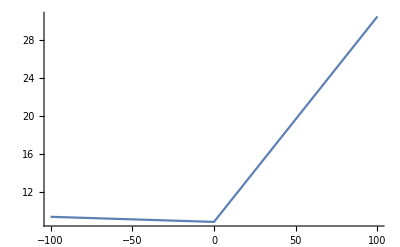

```mathematica
Plot[{h3[x,0.1,0.3,0.1]},{x,100,-100}]
```

```mathematica
s=5;θ=-0.1;g[a_,mrt_,ot_,k1_]:=1/(Sign[a]θ)Log[1/(√(2π))
NIntegrate[Exp[θ Sign[a](a(1+Sign[a]k1)(xx[ot,W,mrt]))-W^2/2],{W,-∞,∞}]]-a
```

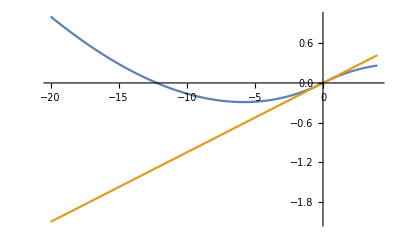

```mathematica
Plot[{g[x,0.1,0.4,0],h[x,0.1,0.4,0]},{x,4,-20},PlotRange->Automatic]
```

```mathematica
xx[ot_,W_,mrt_]:=Exp[ot W+mrt-ot^2/2]
```

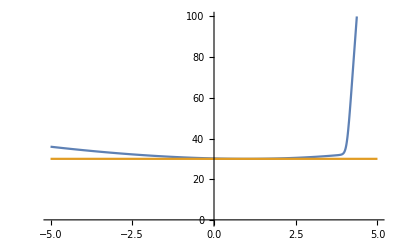

```mathematica
x2[ot_,W_,mrt_,S_,a_,K_,k1_]:=Max[0,K-S xx[ot,W,mrt]]+Min[2000,S a(1+Sign[a]k1)xx[ot,W,mrt]-S a];h2[a_,mrt_,ot_,k1_,S_,K_]:=1/(√(2π))
NIntegrate[x2[ot,W,mrt,S,a,K,k1]Exp[-W^2/2],{W,-∞,∞}];
f[a_,mrt_,ot_,k1_,S_,K_]:=-1/θ Log[1/(√(2π))
NIntegrate[Exp[-θ x2[ot,W,mrt,S,a,K,k1]-W^2/2],{W,-∞,∞}]];
Plot[{f[x,-0,0.2,0,10,40],h2[x,0,0.2,0,10,40]},{x,5,-5},PlotRange->{-1,100}]
```

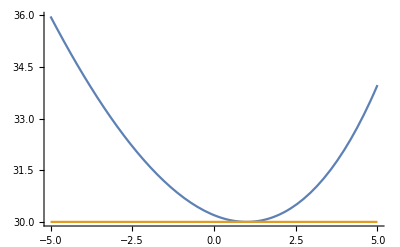

```mathematica
f[1,-0.1,0.2,0,10,40]
```

-10+10. Log[NIntegrate[Exp[-θ x2[0.2,W,-0.1,10,1,40,0]-W^2/2],{W,-∞,∞}]/(√(2 π))]

```mathematica
√(1/12)//N
```

0.288675

## Dateien “pi(H) power” (= “pi(H) exp util):

```mathematica
x2[ot_,W_,mrt_,S_,a_,K_,k1_]:=Max[0,K-S xx[ot,W,mrt]]+Min[10000,S a(1+Sign[a]k1)(xx[ot,W,mrt])];h2[a_,mrt_,ot_,k1_,S_,K_]:=1/(√(2π))
NIntegrate[x2[ot,W,mrt,S,a,K,k1]Exp[-W^2/2],{W,-∞,∞}]-S a;
```

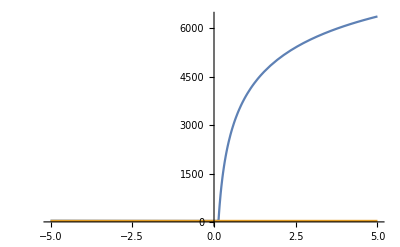

```mathematica
f[a_,mrt_,ot_,k1_,S_,K_]:=-1/θ Log[1/(√(2π))
NIntegrate[Exp[-θ x2[ot,W,mrt,S,a,K,k1]-W^2/2],{W,-∞,∞}]]-S a;
Plot[{f[x,-0,0.2,0,10,40],h2[x,0,0.2,0,10,40]},{x,5,-5}]
```